## Def. de B(Z,A) y M(Z,A) :

```mathematica
c1=15.85; c2=18.34; c3=0.71; c4=23.21; c5=12;
c1*A - c2*A^(3/2)-c3(Z(Z-1))/(A^(1/3))-c4*(A-2Z)^2/A+ (c5/A^(1/2))*(-Mod[Z,2]-Mod[A,2]+1)
```

15.85 A-18.34 A^(3/2)-(23.21 (A-2 Z)^2)/A-(0.71 (-1+Z) Z)/A^(1/3)+(12 (1-Mod[A,2]-Mod[Z,2]))/(√A)

```mathematica
B[Z_,A_]:=15.85 A-18.34 A^(2/3)-(23.21 (A-2 Z)^2)/A-(0.71 (-1+Z) Z)/A^(1/3)+(12 (1-Mod[A,2]-Mod[A-Z,2]))/(√A)
```

```mathematica
c= 1;uma=931.5016;mH=1.007825032*uma; mn=1.008664904*uma; mp=1.00727646677*uma;
M[Z_,A_]:=Z*mH*c^2 + (A-Z)*mn*c^2 - B[Z,A]
```

```mathematica
Clear[A,Z];M[Z,A]
```

18.34 A^(2/3)-15.85 A+(23.21 (A-2 Z)^2)/A+939.573 (A-Z)+938.791 Z+(0.71 (-1+Z) Z)/A^(1/3)-(12 (1-Mod[A,2]-Mod[A-Z,2]))/(√A)

## Ej. 13 Aqui habia q calcular el M(A,Z) en lugar del B(A,Z)... y graficar en funcion de Z para chekar si el minimo se ubica en Z=54 (q es el producto final de la cadena de decaimiento).

```mathematica
Z={52,53,54}; A={131,131,131};{B[Z,A], B[Z,A]/A}
```

{{1102.34,1107.27,1108.42},{8.4148,8.45248,8.46119}}

```mathematica
A=131;
```

```mathematica
Z=52; Clear[BB]; BB=(A-Z)*mn + Z*mH - (A*uma -85.211)
```

1101.88

```mathematica
Z=53; Clear[BB]; BB=(A-Z)*mn + Z*mH - (A*uma -87.445)
```

1103.33

```mathematica
Z=54; Clear[BB]; BB=(A-Z)*mn + Z*mH - (A*uma -88.416)
```

1103.52

## Ej. 12

```mathematica
Z={56,57,58,59,60}; A={140,140,140,140,140};B[Z,A]
```

{1174.41,1175.99,1177.99,1176.37,1175.17}

```mathematica
A=140;
```

```mathematica
teorica=Table[{Z,B[Z,A]},{Z,30,80}];
```

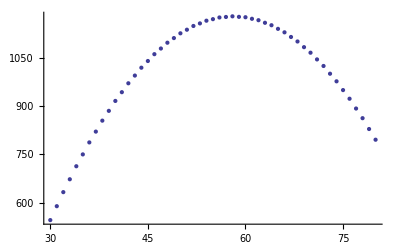

```mathematica
ListPlot[teorica]
```

```mathematica
x={56+57,57+58,58+59}
```

{113,115,117}

```mathematica
y={1.035/(1),3.7605/(1),3.388/(-1)}
```

{1.035,3.7605,-3.388}

```mathematica
data={{113,1.035},{115,3.7605},{117,-3.388}};
```

```mathematica
Clear[x];line = Fit[data, {1,x},x]
```

127.63-1.10575 x

```mathematica
parabola=Table[{Z,-2505+127.63Z-1.10575Z^2},{Z,30,80}];
```

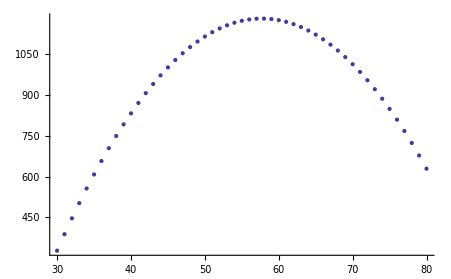

```mathematica
Clear[a,b,c,Z]; ListPlot[parabola]
```

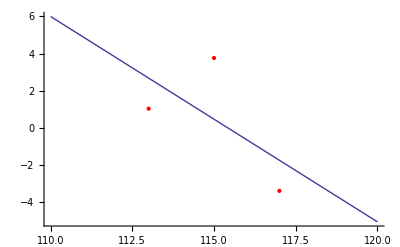

```mathematica
Show[ListPlot[data, PlotStyle->Red], Plot[line, {x, 110, 120}]]
```

```mathematica
ListPlot[{teorica,parabola},PlotStyle->{Blue,Red}]
```

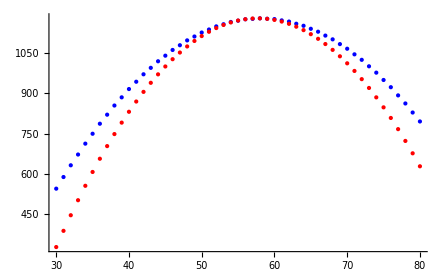

```mathematica
k2=127.63;k3=-1.10575;delta=k2*(-1)+k3*(59^2-60^2)
```

3.95425

## Ej. 14

```mathematica
x=0.5;energia=M[92,235]-2M[92x,235x]
```

177.925

```mathematica
x=1/3;energia=M[92,235]-M[92x,235x]-M[92*(1-x),235*(1-x)]
```

153.035

```mathematica
x=2/3;energia=M[92,235]-M[92x,235x]-M[92*(1-x),235*(1-x)]
```

153.035

```mathematica
Clear[r]; En[r_]:=M[92,235]-M[92*r,235*r]-M[92*(1-r),235*(1-r)]
```

```mathematica
Clear[r];En[r]
```

218922.-2 (698.411 r^(2/3)+217260. r+10.585 r^(2/3) (-1+92 r)-(12 (1-Mod[143 r,2]-Mod[235 r,2]))/(√235 √r))

```mathematica
r=0.1;En[r]
```

32.1305

```mathematica
M[92,235]-M[92r,235r]-M[92*(1-r),235*(1-r)]
```

32.1305

```mathematica
Clear[r];
```

```mathematica
Dt[En[r],r]
```

-2 (217260.+465.608/r^(1/3)+973.819 r^(2/3)+(7.05666 (-1+92 r))/r^(1/3)+(6 (1-Mod[143 r,2]-Mod[235 r,2]))/(√235 r^(3/2))-(12 (-143 Mod^(1,0)[143 r,2]-235 Mod^(1,0)[235 r,2]))/(√235 √r))

```mathematica
PEN[r_]:=-2 (217259.8131868979+465.60751409922193/r^(1/3)+973.8185640717054 r^(2/3)+(7.056656261389169 (-1+92 r))/r^(1/3)+(6 (1-Mod[143 r,2]-Mod[235 r,2]))/(√235 r^(3/2))-(12 (-143 Derivative[1,0][Mod][143 r,2]-235 Derivative[1,0][Mod][235 r,2]))/(√235 √r))
```

```mathematica
PEN[r]
```

-2 (217260.+465.608/r^(1/3)+973.819 r^(2/3)+(7.05666 (-1+92 r))/r^(1/3)+(6 (1-Mod[143 r,2]-Mod[235 r,2]))/(√235 r^(3/2))-(12 (-143 Mod^(1,0)[143 r,2]-235 Mod^(1,0)[235 r,2]))/(√235 √r))

```mathematica
r=1;PEN[r]
```

-439274.

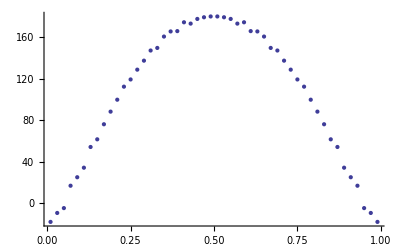

```mathematica
Clear[r];ListPlot[Table[{r,En[r]},{r,.01,1,.02}]]
```

Aqui veo que la maxima energia liberada se da cuando la fraccion "r" es 0.5.

```mathematica
FindRoot[PEN[r],{r,0.05}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function.  You may need more than MachinePrecision digits of working precision to meet these tolerances.

{r→-26.7534-0.0132264 ⅈ}

## Ej. 16

```mathematica
(*Los calculos teoricos y empiricos respectivamente en grupos de a dos: *)
```

```mathematica
2M[1,2]-M[2,3]-mn
```

-11.4223

```mathematica
2(2uma+13.136)-(3uma +14.931) - mn
```

3.26963

```mathematica
2M[1,2]-M[1,3]-mp
```

-2.99854

```mathematica
2(2uma+13.136)-(3uma +14.95) - mp
```

4.54396

```mathematica
M[1,2]+M[1,3]-M[2,4]-mn
```

18.0399

```mathematica
(2uma+13.136)+(3uma+14.95)-(4uma +2.425) - mn
```

17.5896

## Ej. 17

```mathematica
dif=M[29,64]-M[30,64]
```

-0.759533

```mathematica
dif=(64uma-65.421)-(64uma-65.999)
```

0.578